```mathematica
f[x_, y_]:=x*y*Log[x^2+y^2]
```

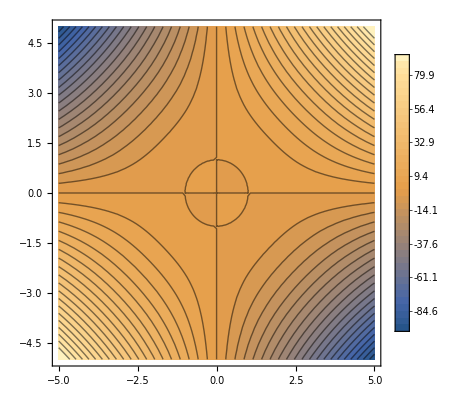

```mathematica
ContourPlot[f[x,y],{x,-5,5},{y,-5,5}, PlotLegends->Automatic, Contours->40]
```

```mathematica
FindMaximum[f[x,y], {{x,-5}, {y,-5}}]
```

FindMaximum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{2.99223×10^212,{x→-7.86474×10^104,y→-7.86474×10^104}}

```mathematica
g = Grad[f[x,y], {x,y}]
```

{(2 x^2 y)/(x^2+y^2)+y Log[x^2+y^2],(2 x y^2)/(x^2+y^2)+x Log[x^2+y^2]}

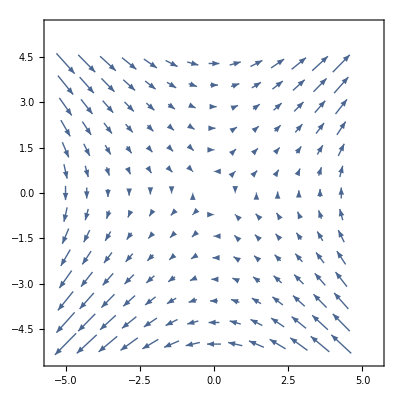

```mathematica
h2 = VectorPlot[g, {x, -5, 5},{y,-5,5}, PlotLegends->Automatic]
```

```mathematica
(*Normal and correct solution*)
```

```mathematica
Clear[f, x, y]
```

```mathematica
f[x_,y_]:=x*y*Log[x^2+y^2]
```

```mathematica
Plot3D[f[x,y], {x,-1,1}, {y,-1,1}]
```

-Graphics3D-

```mathematica
h = ContourPlot[f[x,y], {x,-1,1}, {x,1,1}]
```

ContourPlot::glims: Range specifications {x,-1,1} and {x,1,1} contain the same iteration variable.

```mathematica
ContourPlot[f[x,y],{x,-1,1},{x,1,1}, PlotLegends->Automatic, Contours->40]
```

ContourPlot::glims: Range specifications {x,-1,1} and {x,1,1} contain the same iteration variable.

ContourPlot[f[x,y],{x,-1,1},{x,1,1},PlotLegends→Automatic,Contours→40]

```mathematica
FindMinimum, FindMaximum

(*task 2*)
```

```mathematica
f[x_,y_]:=x^2+x+2y
```

```mathematica
d = ImplicitRegion[{x≤1, y≤1,y≥(x-1)^2},{x,y}]
```

ImplicitRegion[x≤1&&y≤1&&y≥(-1+x)^2,{x,y}]

```mathematica
Plot3D[f[x,y], {x,y}∈d]
```

-Graphics3D-

```mathematica
max=f[1,1]
```

4

```mathematica
min = NMinimize[{f[x,y], {x,y}∈d}, {x,y}]
```

{1.25,{x→0.5,y→0.25}}

```mathematica
h = NMaximize[{f[x,y],{x,y}∈d}, {x,y}]
```

{4.,{x→1.,y→1.}}

```mathematica
Clear[f, x, y]
```

```mathematica
f[x_]:=ⅇ^(-x^2)-1/5
```

```mathematica
(*task 4*)
```

```mathematica
Series[f[x], {x,1,5}]
```

(-1/5+1/ⅇ)-(2 (x-1))/ⅇ+(x-1)^2/ⅇ+(2 (x-1)^3)/(3 ⅇ)-(5 (x-1)^4)/(6 ⅇ)+(x-1)^5/(15 ⅇ)+O[x-1]^6

```mathematica
x0 = 1
```

1

```mathematica
t[n_Integer]:=Series[f[x],{x,x0,n}]//Normal
```

```mathematica
Manipulate[NMaximize[{Abs[Evaluate[t[n]]-f[x]],0<x<2}],{x}]
```

NMaximize::argr: NMaximize called with 1 argument; 2 arguments are expected.

```mathematica
Clear[f, x]
```

```mathematica
(*самостоятельная работа на семинаре*)
```

```mathematica
f[x_]:=Cosh[-x^2]-3
```

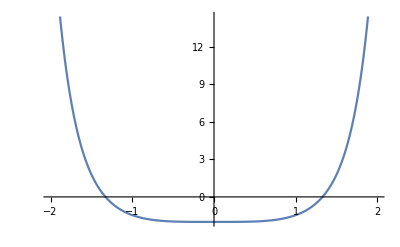

```mathematica
Plot[f[x], {x,-2,2}]
```

```mathematica
Reduce[D[f[x],x]==0,x,Reals]//N
```

x==0.

```mathematica
Reduce[D[f[x]]==0,x,Reals]
```

x==-√ArcCosh[3]||x==√ArcCosh[3]

```mathematica
(*при x <-1.327684892600306 (-√ArcCosh[3]), функция постоянно положительня. При x > 1.327684892600306 (√ArcCosh[3]) - функция Постоянно положительна. При все остальных случаях - (-√ArcCosh[3] < x < √ArcCosh[3]) - функция постонно отрицательна  *)
```

```mathematica
Reduce[f[x]==0, x, Reals]
```

x==-√ArcCosh[3]||x==√ArcCosh[3]

```mathematica
Reduce[f'[x]==0, x, Reals]
```

x==0

```mathematica
(*при x < 0 функция монотонно убывает, при x > 0 функция монотонно возрастает*)
```

```mathematica
Reduce[D[D[f[x],x],x]>0,x,Reals]
```

x≠0

```mathematica
(*функция строго выпуклая вниз в точке во всех точках, кроме x==0*)
```

```mathematica
a = f'[1]
```

2 Sinh[1]

```mathematica
b=f[1]
```

-3+Cosh[1]

```mathematica
t[x_]:= f[1]+f'[1](x-1)
```

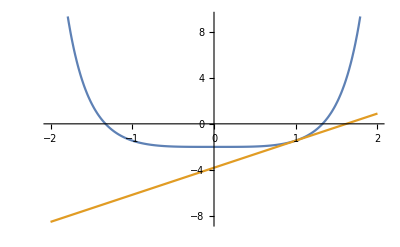

```mathematica
Plot[{f[x], t[x]}, {x,-2,2}] (*касательная*)
```

```mathematica
Limit[f[x]/x,x->∞](*нет наклонных асимптот*)
```

∞